## Undamped oscillator & PID for disturbance rejection & command tracking (Problem 3.2)

```mathematica
Clear["Global`*"];
SetOptions[Plot,PlotRange -> All];
tmax=10;trange={t,0,tmax};d=DiracDelta[t]; (* d = input disturbance *)
step=UnitStep[t]; 
G=ω^2/(s^2+2ζ ω s+ω^2)/.{ζ->0,ω->1}; Gtf=TransferFunctionModel[G,s]; K1=Kp;
```

Proportional control

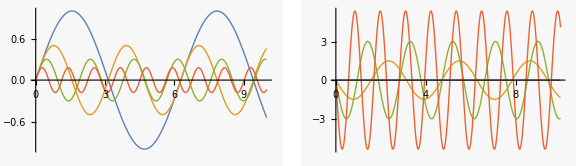

```mathematica
SG1=Together[G/(1+K1 G)]; SG1tf=TransferFunctionModel[SG1,s];
negT1=Together[(-K1 G)/(1+K1 G)]; negT1tf=TransferFunctionModel[negT1,s];
y0=OutputResponse[Gtf,d,trange][[1]]; (* open-loop impulse resp. *)
y1a=OutputResponse[SG1tf/.Kp->3,d,trange][[1]]; 
y1b=OutputResponse[SG1tf/.Kp->10,d,trange][[1]]; y1c=OutputResponse[SG1tf/.Kp->30,d,trange][[1]]; (* closed-loop prop. control *)
p1a=Plot[{y0,y1a,y1b,y1c},{t,0,tmax}];

u1a=OutputResponse[negT1tf/.Kp->3,d,trange][[1]] ;
u1b=OutputResponse[negT1tf/.Kp->10,d,trange][[1]] ; (* [=2(t-1)ⅇ^-t] *)
u1c=OutputResponse[negT1tf/.Kp->30,d,trange][[1]] ; (* [=2(t-1)ⅇ^-t] *)
p1b=Plot[{0,u1a,u1b,u1c},{t,0,tmax}];

GraphicsRow[{p1a, p1b},ImageSize->Large]
```

```mathematica
FullSimplify[{OutputResponse[SG1tf,d,t],OutputResponse[negT1tf,d,t]},Kp>0]//TraditionalForm
```

((t sin(√(Kp+1) t))/(√(Kp+1))
-(Kp t sin(√(Kp+1) t))/(√(Kp+1)))

```mathematica
FullSimplify[DSolveValue[{y''[t]+y[t]==-Kp y[t]+d,y[0]==0,y'[0]==0},y[t],t],Kp>0]//TraditionalForm
```

((t-0) sin(√(Kp+1) t))/(√(Kp+1))

```mathematica
{SG1,negT1}
```

{1/(1+Kp+s^2),-Kp/(1+Kp+s^2)}

Pure derivative control

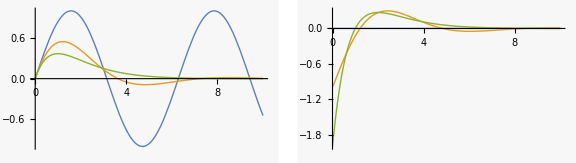

```mathematica
K2=Kd s; SG2=Together[G/(1+K2 G)]; SG2tf=TransferFunctionModel[SG2,s];
negT2=Together[(-K2 G)/(1+K2 G)]; negT2tf=TransferFunctionModel[negT2,s];
y2a=OutputResponse[SG2tf/.Kd->1,d,trange][[1]] ;
y2b=OutputResponse[SG2tf/.Kd->2,d,trange][[1]]; 
p2a=Plot[{y0,y2a,y2b},{t,0,tmax}];

u2a=OutputResponse[negT2tf/.Kd->1,d,trange][[1]] ;
u2b=OutputResponse[negT2tf/.Kd->2,d,trange][[1]] ; (* [=2(t-1)ⅇ^-t] *)
p2b=Plot[{0,u2a,u2b},{t,0,tmax}];

GraphicsRow[{p2a, p2b},ImageSize->Large]
```

```mathematica
{SG2,negT2,Limit[s negT2,s -> ∞]}  (* = u(0^+) the initial value of the output *)
```

{1/(1+Kd s+s^2),-(Kd s)/(1+Kd s+s^2),-Kd}

```mathematica
{OutputResponse[SG2tf/.Kd->1,d,t],OutputResponse[negT2tf/.Kd->1,d,t],OutputResponse[SG2tf/.Kd->2,d,t],OutputResponse[negT2tf/.Kd->2,d,t]}//Simplify//TraditionalForm
```

((2 ⅇ^(-t/2) t sin((√3 t)/2))/(√3)
1/3 ⅇ^(-t/2) t (√3 sin((√3 t)/2)-3 cos((√3 t)/2))
ⅇ^-t t t
2 ⅇ^-t (t-1) t)

```mathematica
eqs2={y''[t]+y[t]==u[t]+d,u[t]==-Kd y'[t],y[0]==0,y'[0]==0}/.Kd->2;
DSolveValue[eqs2,{y[t],u[t]},t]//Simplify//TraditionalForm
```

{ⅇ^-t t (t-0),-2 ⅇ^-t (t-1) (0-t)}

PD control

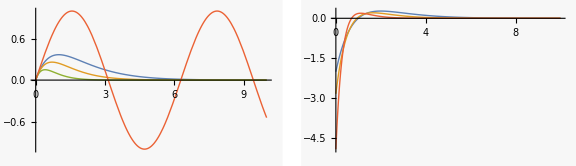

```mathematica
K3=Kp+Kd s; SG3=Together[G/(1+K3 G)]; SG3tf=TransferFunctionModel[SG3,s];
negT3=Together[(-K3 G)/(1+K3 G)]; negT3tf=TransferFunctionModel[negT3,s];
 y3a=OutputResponse[SG3tf/.{Kp->1,Kd->2 √2},d,trange][[1]] ;
y3b=OutputResponse[SG3tf/.{Kp->5,Kd->2 √6},d,trange][[1]]; 
p3a=Plot[{y2b,y3a,y3b,y0},{t,0,tmax}];

u3a=OutputResponse[negT3tf/.{Kp->1,Kd->2 √2},d,trange][[1]] ;
u3b=OutputResponse[negT3tf/.{Kp->5,Kd->2 √6},d,trange][[1]] ;
p3b=Plot[{u2b,u3a,,u3b},{t,0,tmax}];

GraphicsRow[{p3a, p3b},ImageSize->Large]
```

```mathematica
{SG3,negT3,Limit[s negT3,s -> ∞],Limit[ negT3,s -> 0]}  (* = u(0^+), the initial value of the output *)
```

{1/(1+Kp+Kd s+s^2),(-Kp-Kd s)/(1+Kp+Kd s+s^2),-Kd,-Kp/(1+Kp)}

```mathematica
{SG3,negT3}/.Kd->2 √(Kp+1)//FullSimplify//TraditionalForm
```

{1/(2 √(Kp+1) s+Kp+s^2+1),-(2 √(Kp+1) s+Kp)/(2 √(Kp+1) s+Kp+s^2+1)}

```mathematica
{OutputResponse[SG3tf/.Kd->2 √(Kp+1),d,t],OutputResponse[negT3tf/.Kd->2 √(Kp+1),d,t]}//Simplify//TraditionalForm
```

(t t ⅇ^(-√(Kp+1) t)
t ⅇ^(-√(Kp+1) t) ((Kp+2) t-2 √(Kp+1)))

```mathematica
eqs3={y''[t]+y[t]==-Kp y[t]-Kd y'[t]+d,y[0]==0,y'[0]==0}/.Kd->2 √(Kp+1);
{ysol1,usol1}=DSolveValue[eqs3,{y[t],-Kp y[t]-Kd y'[t]}/.Kd->2 √(Kp+1),t]//Simplify;
{ysol1,usol1}/.{Kp->1}//TraditionalForm
```

{ⅇ^(-√2 t) t (t-0),ⅇ^(-√2 t) (2 √2-3 t) (0-t)}

PD control does not reject a step disturbance

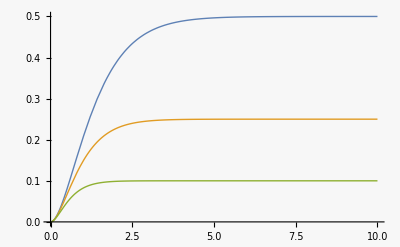

```mathematica
y3c=OutputResponse[SG3tf/.{Kp->1,Kd->2 √2},step,trange][[1]] ;
 y3d=OutputResponse[SG3tf/.{Kp->3,Kd->2 √4},step,trange][[1]] ;
y3e=OutputResponse[SG3tf/.{Kp->9,Kd->2 √10},step,trange][[1]] ;
p3c=Plot[{y3c,y3d,y3e},{t,0,tmax}]
```

```mathematica
{SG3,Limit[SG3,s->0]}  (* SG3(0) gives the step response for t->∞ *)
```

{1/(1+Kp+Kd s+s^2),1/(1+Kp)}

```mathematica
(* ysol=OutputResponse[SG3tf/.Kd->2 √(Kp+1),step,t][[1]]//FullSimplify//TraditionalForm *)
```

PID control:  needed to reject a step disturbance

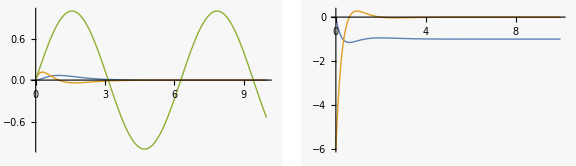

```mathematica
K4=Kp+Ki/s+Kd s; SG4=Together[G/(1+K4 G)]; SG4tf=TransferFunctionModel[SG4,s];
negT4=Together[(-K4 G)/(1+K4 G)]; negT4tf=TransferFunctionModel[negT4,s];
 y4a=OutputResponse[SG4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},step,trange][[1]] ;
 y4b=OutputResponse[SG4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},d,trange][[1]] ;
p4a=Plot[{y4a,y4b,y0},{t,0,tmax}];

u4a=OutputResponse[negT4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},step,trange][[1]] ;
u4b=OutputResponse[negT4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},d,trange][[1]] ;
p4b=Plot[{u4a,u4b},{t,0,tmax}];

GraphicsRow[{p4a, p4b},ImageSize->Large]
```

```mathematica
{SG4,negT4}
```

{s/(Ki+s+Kp s+Kd s^2+s^3),(-Ki-Kp s-Kd s^2)/(Ki+s+Kp s+Kd s^2+s^3)}

```mathematica
{SG4,negT4}//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2}//Simplify
```

{s/(2+s)^3,-(8+11 s+6 s^2)/(2+s)^3}

```mathematica
{OutputResponse[SG4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},d,t]//TraditionalForm,
OutputResponse[SG4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},step,t]//TraditionalForm}
```

{{-ⅇ^(-2 t) (t-1) t t},{1/2 ⅇ^(-2 t) t^2 t}}

```mathematica
{OutputResponse[negT4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},d,t]//Simplify//TraditionalForm,
OutputResponse[negT4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},step,t]//Simplify//TraditionalForm}
```

{{-ⅇ^(-2 t) (5 t^2-13 t+6) t},{-1/2 ⅇ^(-2 t) (-5 t^2+8 t+2 ⅇ^(2 t)-2) t}}

PID control:  look at command tracking (step response)

```mathematica
T4=Together[(K4 G)/(1+K4 G)]; T4tf=TransferFunctionModel[T4,s];
SK4=Together[K4/(1+K4 G)];SK4tf=TransferFunctionModel[SK4,s];
```

NDSolve::irfail: Unable to reduce the index of the system to 0 or 1.

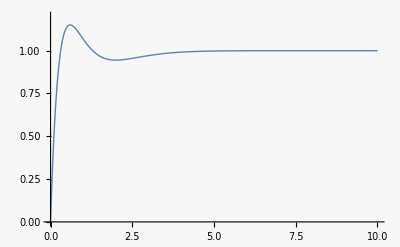

```mathematica
ypid=OutputResponse[T4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},step,trange][[1]] ;
upid=OutputResponse[SK4tf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},step,trange][[1]] ;
Plot[{ypid,upid},{t,0,tmax},PlotRange->{0,1.2}]
```

```mathematica
{K4,T4,SK4}//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2}//Simplify
```

{11+8/s+6 s,(8+11 s+6 s^2)/(2+s)^3,((1+s^2) (8+11 s+6 s^2))/(2+s)^3}

```mathematica
T4tfa =T4tf /.{Kp->3 a^2-1,Ki->a^3,Kd->3a}/.a->2//Simplify
```

(8+11 s+6 s^2)/(2+s)^3TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11821FalseFalseFalseAutomaticNoneAutomatic

```mathematica
ytest=OutputResponse[T4tfa,step,t][[1]] //FullSimplify; ytest//TraditionalForm
```

1/2 ⅇ^(-2 t) ((8-5 t) t-2) t+t

```mathematica
Limit[D[ytest,t],t->0]
```

Indeterminate

```mathematica
SK4tfa=SK4tf/.{Kp->3 a^2-1,Ki->a^3,Kd->3a}/.a->2//Simplify
```

((1+s^2) (8+11 s+6 s^2))/(2+s)^3TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
utest=OutputResponse[SK4tfa,1,t][[1]] //FullSimplify; utest//TraditionalForm
```

ⅇ^(-2 t) (5/2 (16-5 t) t-26)+1

PID control: command tracking (step response), with feedforward

```mathematica
F4=1/(T4 (1+s/a)^2); (* the feedforward element F4 needs to be biproper *)
```

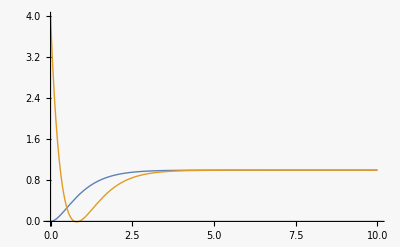

```mathematica
T4a=F4 T4;
T4atf=TransferFunctionModel[T4a,s];
SFK4=SK4 F4; SFK4tf=TransferFunctionModel[SFK4,s];


ypida=OutputResponse[T4atf//.{Kp->3 a^2-1,Ki->a^3,Kd->3a,a->2},step,trange][[1]] ;
upida=OutputResponse[SFK4tf/.a->2,step,trange][[1]] ;
Plot[{ypida,upida},{t,0,tmax}]
```

```mathematica
{T4atf,SFK4}/.a->2//Simplify
```

{4/(2+s)^2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11421FalseFalseFalseAutomaticNoneAutomatic,(4 (1+s^2))/(2+s)^2}

```mathematica
{OutputResponse[T4atf/.a->2,step,t][[1]],OutputResponse[SFK4tf/.a->2,step,t]} //FullSimplify//TraditionalForm
```

{t-ⅇ^(-2 t) (2 t+1) t,{ⅇ^(-2 t) (-10 t+ⅇ^(2 t)+3) t}}